{{X1→InterpolatingFunction[…],X2→InterpolatingFunction[…],M11→InterpolatingFunction[…],M12→InterpolatingFunction[…],M21→InterpolatingFunction[…],M22→InterpolatingFunction[…]}}

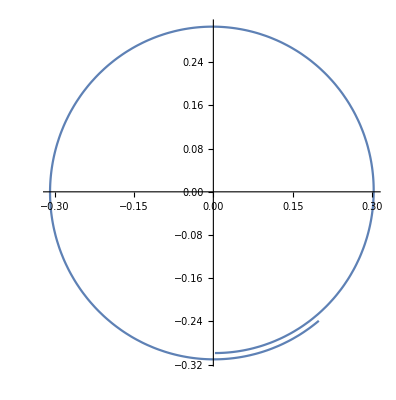

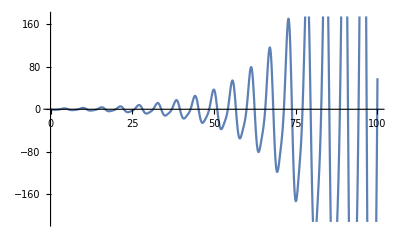

{0.316228}

5.712

{{0.396342},{-0.77444},{-0.0290587},{1.29654}}

```mathematica
system={X1'[t]==X1[t]/10-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,
X2'[t]==X1[t]+X2[t]/10+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t],
M11'[t]==M11[t]*(-3*X1[t]^2-2*X1[t]*X2[t]-X2[t]^2+1/10)+M21[t]*(-X1[t]^2-2*X1[t]*X2[t]-3*X2[t]^2-1),
M12'[t]==M12[t]*(-3*X1[t]^2-2*X1[t]*X2[t]-X2[t]^2+1/10)+M22[t]*(-X1[t]2-2*X1[t]*X2[t]-3*X2[t]^2-1),
M21'[t]==M11[t]*(3*X1[t]^2-2*X1[t]*X2[t]+X2[t]^2+1)+M21[t]*(-X1[t] ^2+2*X1[t]*X2[t]-3*X2[t]^2+1/10),
M22'[t]==M12[t]*(3*X1[t]^2-2*X1[t]*X2[t]+X2[t]^2+1)+M22[t]*(-X1[t]^2+2*X1[t]*X2[t]-3*X2[t]^2+1/10)};
sol=NDSolve[{system,X1[0]==X2[0]==0.2,M11[0]==M22[0]==1,M12[0]==M21[0]==0},{X1,X2,M11,M12,M21,M22},{t,1000}]
ParametricPlot[Evaluate[{X1[t],X2[t]}/.sol],{t,3.62850988532908,10}]
Plot[Evaluate[M12[t]/.sol],{t,0,100}]


system1={X1'[t]==X1[t]/10-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,
X2'[t]==X1[t]+X2[t]/10+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t]};
stableLimitCycleRadius=Sqrt[Evaluate[X1[200]/.sol]^2+Evaluate[X2[200]/.sol]^2]
(*NDSolve[{X1[t]/.sol==tmp,X1[0]==X2[0]==0.2},{X1,X2},{t,50}]*)
{s1,{{x0},{y0}}}=Reap[
NDSolve[{system1,
X1[0]==X2[0]==0.2,WhenEvent[X1'[t]>0,Sow[t,"x"]],(*minima of x*)
WhenEvent[X2'[t]>0,Sow[t,"y"]]},(*minima of y*)
{X1[t],X2[t]},{t,0,50}],{"x","y"}];
tab=Table[Mean@Differences@min[[-Round[Length@min/4];;]],{min,{x0,y0}}];
period=First[tab]

startValue=60;
MforCycle={Evaluate[M11[period]/.sol],Evaluate[M12[period]/.sol],Evaluate[M21[period]/.sol],Evaluate[M22[period]/.sol]}
(*MforCycle={Evaluate[M11[startValue+period]/.sol],Evaluate[M12[startValue+period]/.sol],Evaluate[M21[startValue+period]/.sol],Evaluate[M22[startValue+period]/.sol]}*)
(*FindRoot[(X1[t]^2/.sol+X2[t]^2/.sol)==tmp,{t,1,200}]*)
```

```mathematica
(* Calculations for 1e)*)
firstSystem={r'[t]==r[t]/10-r[t]^3,
theta'[t]== 1+r[t]^2,
M11'[t]== M11[t](1/10-3r[t]^2),
M12'[t]==0,
M21'[t]== 2M21[t]r[t],
M22'[t]== 0}
DSolve[{firstSystem,r[0]=0.1,theta[0]=1.01},{r,theta,M11,M12,M21,M22},t]
A={r[t],theta[t]};
D[firstSystem,{A}][[2]];

JM={{1/10-3r[t]^2,0},{2r[t],0}}*{{M11[t],M12[t]},{M21[t],M22[t]}}
```

{r'[t]==r[t]/10-r[t]^3,theta'[t]==1+r[t]^2,M11'[t]==M11[t] (1/10-3 r[t]^2),M12'[t]==0,M21'[t]==2 M21[t] r[t],M22'[t]==0}

DSolve::deqn: Equation or list of equations expected instead of 0.1 in the first argument {{r'[t]==r[t]/10-r[t]^3,theta'[t]==1+r[t]^2,M11'[t]==M11[t] (1/10-3 r[«1»]^2),M12'[t]==0,M21'[t]==2 M21[t] r[t],M22'[t]==0},0.1,1.01}.

DSolve[{{r'[t]==r[t]/10-r[t]^3,theta'[t]==1+r[t]^2,M11'[t]==M11[t] (1/10-3 r[t]^2),M12'[t]==0,M21'[t]==2 M21[t] r[t],M22'[t]==0},0.1,1.01},{r,theta,M11,M12,M21,M22},t]

{{M11[t] (1/10-3 r[t]^2),0},{2 M21[t] r[t],0}}

```mathematica
system={x'[t]== 10(y[t]-x[t]),
y'[t]== 28x[t]-y[t]-x[t]z[t],
z'[t]== x[t]y[t]-8/3 z[t]};

parameters={{b-> 8/3},{sigma-> 10},{r-> 28}};
```

```mathematica
sol=NDSolve[{system,x[0]== y[0]==z[0]== 1},{x,y,z},{t,200}];

ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,1,40}]
```

-Graphics3D-